# Изпит по КЧМ, И4, РБ, Име: Мкртич Чивиджян, Фак. № 2001261044

## Задача 1:

Условие: (√(x^3)- (1+4+4)sin(x))/(1+cos^2(x))-3(4+4+2)=0

### a)

```mathematica
f[x_]:=(√(x^3)-(1+4+4)Sin[x])/(1+Cos[x]^2)-3(4+4+2)
```

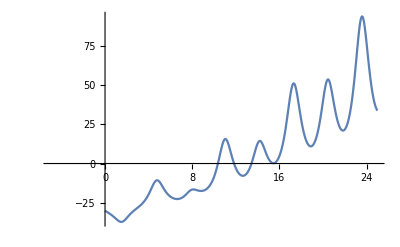

```mathematica
Plot[f[x],{x,-5,25}]
```

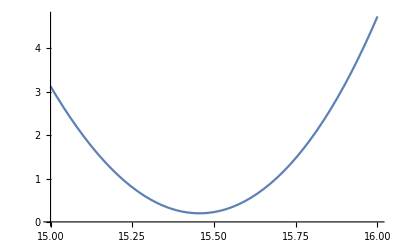

```mathematica
Plot[f[x],{x,15,16}]
```

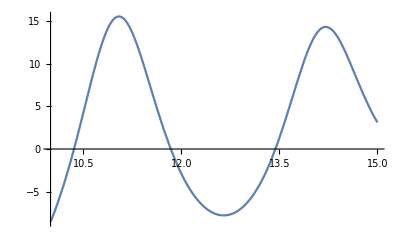

```mathematica
Plot[f[x],{x,10,15}]
```

Брой корени: 2

### б)

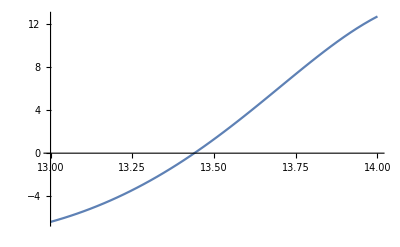

```mathematica
Plot[f[x], {x, 13, 14}]
```

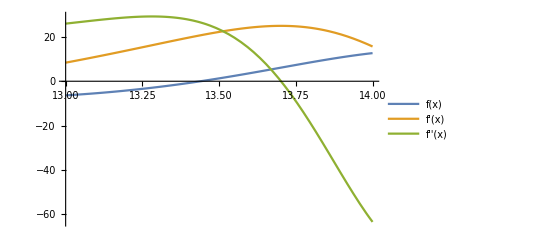

```mathematica
Plot[{f[x], f'[x], f''[x]}, {x, 13, 14}, PlotLegends->"Expressions"]
```

```mathematica
f[13.]
```

-6.36873

```mathematica
f[14.]
```

12.6699

Извод:
(1) Функцията f(x) е непрекъсната, защото е сума от непрекъснати функции 
(2). f(13) = -6.36873 < 0 
 f(14) = 12.6699 > 0
Функцията има различни знаци в двата края на разглеждания интервал [13; 14].
Следователно от (1) и (2) следва, че в интервала [13; 14] функцията има поне един
корен.

### в) 4 итерации

```mathematica
func[x_]:= (√(x^3)-(1+4+4)Sin[x])/(1+Cos[x]^2)-3(4+4+2)

For[
(*Начални условия*)
n = 0; a=13.; b=14.,
n<=4,n++,
(*Тяло на цикъла*)
Print["|","n = ",n,"| a_n = ",a,"| b_n = ",b,"| m_n = ",m=(a+b)/2,"| f(m_n) = ",func[m],"| ε_n = ",(b-a)/2,"|"];
If[func[m]<0,a=m,b=m]
]
```

|n = 0| a_n = 13.| b_n = 14.| m_n = 13.5| f(m_n) = 1.29267| ε_n = 0.5|

|n = 1| a_n = 13.| b_n = 13.5| m_n = 13.25| f(m_n) = -3.42634| ε_n = 0.25|

|n = 2| a_n = 13.25| b_n = 13.5| m_n = 13.375| f(m_n) = -1.2856| ε_n = 0.125|

|n = 3| a_n = 13.375| b_n = 13.5| m_n = 13.4375| f(m_n) = -0.0481029| ε_n = 0.0625|

|n = 4| a_n = 13.4375| b_n = 13.5| m_n = 13.4688| f(m_n) = 0.610015| ε_n = 0.03125|

### г)

Приближението  е m_n = 13.4688  с точност 0.03125.

### д)

```mathematica
func[x_]:=(√(x^3)-(1+4+4)Sin[x])/(1+Cos[x]^2)-3(4+4+2)

epszad=0.0000001;
eps=100;
For[
(*Начални условия*)
n = 0; a=13.; b=14.,
eps>epszad,n++,
(*Тяло на цикъла*)
Print["|","n = ",n,"| a_n = ",SetPrecision[a,10],"| b_n = ",SetPrecision[b,10],"| m_n = ",SetPrecision[m=(a+b)/2,10],"| f(m_n) = ",func[m],"| ε_n = ",eps=(b-a)/2,"|"];
If[func[m]<0,a=m,b=m]
]
```

|n = 0| a_n = 13.| b_n = 14.| m_n = 13.5| f(m_n) = 1.29267| ε_n = 0.5|

|n = 1| a_n = 13.| b_n = 13.5| m_n = 13.25| f(m_n) = -3.42634| ε_n = 0.25|

|n = 2| a_n = 13.25| b_n = 13.5| m_n = 13.375| f(m_n) = -1.2856| ε_n = 0.125|

|n = 3| a_n = 13.375| b_n = 13.5| m_n = 13.4375| f(m_n) = -0.0481029| ε_n = 0.0625|

|n = 4| a_n = 13.4375| b_n = 13.5| m_n = 13.46875| f(m_n) = 0.610015| ε_n = 0.03125|

|n = 5| a_n = 13.4375| b_n = 13.46875| m_n = 13.453125| f(m_n) = 0.277795| ε_n = 0.015625|

|n = 6| a_n = 13.4375| b_n = 13.453125| m_n = 13.4453125| f(m_n) = 0.114045| ε_n = 0.0078125|

|n = 7| a_n = 13.4375| b_n = 13.4453125| m_n = 13.44140625| f(m_n) = 0.0327697| ε_n = 0.00390625|

|n = 8| a_n = 13.4375| b_n = 13.44140625| m_n = 13.43945313| f(m_n) = -0.00771711| ε_n = 0.00195313|

|n = 9| a_n = 13.43945313| b_n = 13.44140625| m_n = 13.44042969| f(m_n) = 0.0125137| ε_n = 0.000976563|

|n = 10| a_n = 13.43945313| b_n = 13.44042969| m_n = 13.43994141| f(m_n) = 0.00239513| ε_n = 0.000488281|

|n = 11| a_n = 13.43945313| b_n = 13.43994141| m_n = 13.43969727| f(m_n) = -0.00266178| ε_n = 0.000244141|

|n = 12| a_n = 13.43969727| b_n = 13.43994141| m_n = 13.43981934| f(m_n) = -0.000133523| ε_n = 0.00012207|

|n = 13| a_n = 13.43981934| b_n = 13.43994141| m_n = 13.43988037| f(m_n) = 0.00113075| ε_n = 0.0000610352|

|n = 14| a_n = 13.43981934| b_n = 13.43988037| m_n = 13.43984985| f(m_n) = 0.000498603| ε_n = 0.0000305176|

|n = 15| a_n = 13.43981934| b_n = 13.43984985| m_n = 13.43983459| f(m_n) = 0.000182537| ε_n = 0.0000152588|

|n = 16| a_n = 13.43981934| b_n = 13.43983459| m_n = 13.43982697| f(m_n) = 0.0000245063| ε_n = 7.62939×10^-6|

|n = 17| a_n = 13.43981934| b_n = 13.43982697| m_n = 13.43982315| f(m_n) = -0.0000545085| ε_n = 3.8147×10^-6|

|n = 18| a_n = 13.43982315| b_n = 13.43982697| m_n = 13.43982506| f(m_n) = -0.0000150011| ε_n = 1.90735×10^-6|

|n = 19| a_n = 13.43982506| b_n = 13.43982697| m_n = 13.43982601| f(m_n) = 4.75261×10^-6| ε_n = 9.53674×10^-7|

|n = 20| a_n = 13.43982506| b_n = 13.43982601| m_n = 13.43982553| f(m_n) = -5.12425×10^-6| ε_n = 4.76837×10^-7|

|n = 21| a_n = 13.43982553| b_n = 13.43982601| m_n = 13.43982577| f(m_n) = -1.85822×10^-7| ε_n = 2.38419×10^-7|

|n = 22| a_n = 13.43982577| b_n = 13.43982601| m_n = 13.43982589| f(m_n) = 2.28339×10^-6| ε_n = 1.19209×10^-7|

|n = 23| a_n = 13.43982577| b_n = 13.43982589| m_n = 13.43982583| f(m_n) = 1.04879×10^-6| ε_n = 5.96046×10^-8|

Извод: за достигане на точност 0.0000001 за нужни 23 итерации

### е)

#### Определяне на постоянните величини M_2 = ?, m_1=?

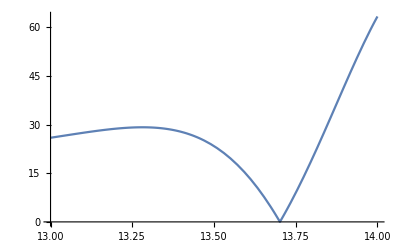

```mathematica
Plot[Abs[f''[x]],{x,13,14}]
```

```mathematica
M2=Abs[f''[14.]]
```

63.3692

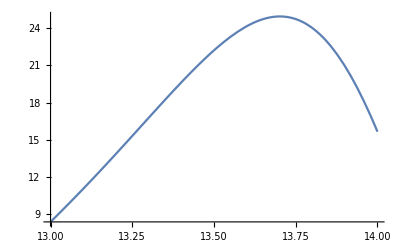

```mathematica
Plot[Abs[f'[x]],{x,13,14}]
```

```mathematica
m1=Abs[f'[13.]]
```

8.36955

```mathematica
P=M2/(2m1)
```

3.7857

#### Извършване на итерациите

```mathematica
f[x_]:=(√(x^3)-(1+4+4)Sin[x])/(1+Cos[x]^2)-3(4+4+2)
x0=0.72;
M2=Abs[f''[0.72]];
m1=Abs[f'[0.7]];
P=M2/(2m1);
Print["n = ",0, " x_n = ", x0, "f(x_n) = ",f[x0],"f'(x_n) = ",f'[x0]]
For[n=1,n<=4,n++,
x1=x0-f[x0]/f'[x0];
eps=P*Abs[x1-x0]^2;
x0=x1;
Print["n = ",n, " x_n = ", x0, " f(x_n) = ",f[x0]," f'(x_n) = ", f'[x0]," ε_n= ", eps]
]
```

n = 0 x_n = 0.72f(x_n) = -33.4012f'(x_n) = -5.66413

n = 1 x_n = -5.17696 f(x_n) = -36.7009+9.80986 ⅈ f'(x_n) = -7.82898+3.70258 ⅈ ε_n= 10.5219

n = 2 x_n = -9.49222-0.787806 ⅈ f(x_n) = -28.2119-13.3591 ⅈ f'(x_n) = -7.1677+1.24059 ⅈ ε_n= 5.8222

n = 3 x_n = -13.0005-3.25882 ⅈ f(x_n) = -30.0125+0.529339 ⅈ f'(x_n) = 0.399645-0.250541 ⅈ ε_n= 5.57163

n = 4 x_n = 41.5059+29.5872 ⅈ f(x_n) = -30.+2.00257×10^-12 ⅈ f'(x_n) = -2.00257×10^-12-1.57087×10^-12 ⅈ ε_n= 1225.38

```mathematica
Precision[eps]
```

MachinePrecision

```mathematica
%//N
```

15.9546